# Passed Functions

```mathematica
ClearAll[$BaseSpacerSize, $BaseObjectSize, LevelSpacerFunction, LevelSpacerSize,LevelSizeFunction,LevelObjectSize, ColorElementsByLevel]
$BaseSpacerSize=1;
$BaseObjectSize=1;

LevelSpacerFunction[level_Integer,levelData_:{}]:=$BaseSpacerSize /level;
LevelSpacerSize[level_Integer, levelData_:{}, spacerFunction_:LevelSpacerFunction]:=spacerFunction[level, levelData];

LevelSizeFunction[level_Integer, levelData_:{}]:=$BaseObjectSize ;
LevelObjectSize[level_Integer, levelData_:{}, sizeFunction_:LevelSizeFunction]:=sizeFunction[level, levelData];

NumberOfElements[data_]:=1/;Not[ListQ[data]]
NumberOfElements[data_List]:=Total[Map[NumberOfElements,data]]

Options[ColorElementsByLevel]={"ColorGradient"->"DeepSeaColors"};
ColorElementsByLevel[data_List, opt:OptionsPattern[]]:=ColorElementsByLevel[data,Depth[data],0,opt]
ColorElementsByLevel[data_,max_, level_,opt: OptionsPattern[]]:=ColorData[OptionValue["ColorGradient"]][level/max]/;Not[ListQ[data]]
ColorElementsByLevel[data_List,max_, level_:1,opt:OptionsPattern[]]:=Map[ColorElementsByLevel[#,max,level+1,opt]&,data]
```

## Functioning version

```mathematica
ClearAll[SpacingOfElements, AggregateTo,LeftFirstTreeTraversalSpacing]

SpacingOfElements[element_, level_:1,SpacingFunction_:LevelSpacerFunction,SizingFunction_:LevelSizeFunction]:=
LevelSizeFunction[level,element]+SpacingFunction[level-1]/;Not[ListQ[element]]

SpacingOfElements[data_List,level_:1,SpacingFunction_:LevelSpacerFunction,SizingFunction_:LevelSizeFunction]:=Map[SpacingOfElements[#,level+1,SpacingFunction,SizingFunction]&,data]
```

```mathematica
data={1,{2},1}
```

{1,{2},1}

```mathematica
s=SpacingOfElements[data]
```

{2,{3/2,3/2,{4/3,4/3},3/2},{3/2,{4/3,{5/4,5/4},4/3}},2}

```mathematica
data={1,{2,2,{3,3},2},{2,{3,{4,4},3}},1};
(*s=SpacingOfElements[data,1,z]*)
s=SpacingOfElements[data]
fs=Flatten[s]
(*afs=Table[AggregateTo[fs,i],{i,Length[fs]}]; afs-=First@afs*)
lfs=With[{fl=FoldList[Plus,fs]},fl-First@fl];
(*afs==lfs*)
Differences@afs
colors=Flatten[ColorElementsByLevel[data,Depth[data]]];
graphicsData=Partition[Flatten[Riffle[Partition[Riffle[Flatten[data],afs],{2}],colors]],{3}];
Graphics@Join[
(*Table[{Blue,Rectangle[{afs[[i]],0},{afs[[i+1]],0.5}]},{i,(Length@afs)-1}]*)
{}
,
({#[[3]],Rectangle[{#[[2]],0},{#[[2]]+1,#[[1]]}]}&/@graphicsData)
]
```

{2,{3/2,3/2,{4/3,4/3},3/2},{3/2,{4/3,{5/4,5/4},4/3}},2}

{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2}

{-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},1]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},2],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},2]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},3],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},3]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},4],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},4]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},5],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},5]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},6],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},6]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},7],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},7]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},8],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},8]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},9],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},9]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},10],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},10]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},11],-AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},11]+AggregateTo[{2,3/2,3/2,4/3,4/3,3/2,3/2,4/3,5/4,5/4,4/3,2},12]}

-Graphics-

```mathematica
$BaseSpacerSize=1;
$BaseObjectSize=1;
LevelSpacerFunction[level_Integer,levelData_:{}]:=$BaseSpacerSize /level;
LevelSizeFunction[level_Integer, levelData_:{}]:=$BaseObjectSize ;

ClearAll[ListLevels, Render, ApplySpacing, ApplySizing,ApplyTranslations]
ListLevels[list_List,level_Integer:0]:=LeveledList["data"-> Replace[list,x_List:>ListLevels[x,level+1],1],"level"-> level+1]
LeveledList[data___][request_]:=Association[data][request]

(*Render[
leveled_LeveledList,
SpacingFunction_:LevelSpacerFunction,
SizingFunction_:LevelSizeFunction,
HorizontalQ_:True]:=With[
{
coordinates=If[
HorizontalQ,
{SpacingFunction[leveled["level"],leveled["data"]], 0},
{0,SpacingFunction[leveled["level"],leveled["data"]]}
]
},
Translate[Replace[leveled,x_LeveledList:>Render[x],{1,Infinity}],coordinates]
]

*)

(*ApplySpacing[leveled_LeveledList,
SpacingFunction_:LevelSpacerFunction,
HorizontalQ_:True]:=With[
{
spacingCoordinates=If[
HorizontalQ,
{SpacingFunction[leveled["level"],leveled["data"]], 0},
{0,SpacingFunction[leveled["level"],leveled["data"]]}
]
},
Translate[Replace[leveled,{x_LeveledList:>ApplySpacing[x]},{1,Infinity}],spacingCoordinates]
]

ApplySizing[leveled___,
SizingFunction_:LevelSizeFunction,
HorizontalQ_:True]:=With[
{
sizingCoordinates=If[
HorizontalQ,
{SizingFunction[leveled["level"],leveled["data"]], 0},
{0,SizingFunction[leveled["level"],leveled["data"]]}
]
},
Replace[leveled,list_List:>Map[Translate[#,sizingCoordinates]&,list],All]
]*)

ApplyTranslations[
leveled_LeveledList,
SpacingFunction_:LevelSpacerFunction,
SizingFunction_:LevelSizeFunction,
HorizontalQ_:True]:=With[
{
spacingCoordinates=If[
HorizontalQ,
{SpacingFunction[leveled["level"],leveled["data"]], 0},
{0,SpacingFunction[leveled["level"],leveled["data"]]}
],
sizingCoordinates=If[
HorizontalQ,
{SizingFunction[leveled["level"],leveled["data"]], 0},
{0,SizingFunction[leveled["level"],leveled["data"]]}
]
},
SpacingTranslate[Replace[leveled,{x_LeveledList:>ApplyTranslations[x], list_List:>Map[SizingTranslate[#,sizingCoordinates]&,list]},{1,Infinity}],spacingCoordinates]
]

Clean[data___]:=Replace[data,ll_LeveledList:> Clean[ll["data"]],{1,Infinity}]

(*Render[leveled_LeveledList]:=Translate[Replace[leveled,x_LeveledList:>Render[x],{1,Infinity}],{a,b}]*)
```

```mathematica
x=ListLevels[{1,2}]
y=ApplyTranslations[x]
z=Clean[y]
```

LeveledList[data→{1,2},level→1]

SpacingTranslate[LeveledList[data→{SizingTranslate[1,{1,0}],SizingTranslate[2,{1,0}]},level→1],{1,0}]

SpacingTranslate[{SizingTranslate[1,{1,0}],SizingTranslate[2,{1,0}]},{1,0}]

```mathematica
Replace[z,
{
SizingTranslate[d_,{a_,b_}]:>Translate[ Rectangle[{0,b},{a,b+d}],{}],
SpacingTranslate[st_,coord_List]:> Translate[st,coord]
}
,All]
```

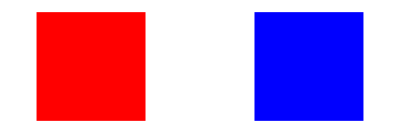

```mathematica
Graphics[Translate[{{Red,Translate[Rectangle[{0,0},{1,1}],{0,0}]},{Blue,Translate[Rectangle[{0,0},{1,1}],{2,0}]}},{0,0}]]
```

```mathematica
x=ListLevels[{1,{2,3},4}]
y=ApplySpacing[x]
z=ApplySizing[y]
```

LeveledList[data→{1,LeveledList[data→{2,3},level→2],4},level→1]

Translate[LeveledList[data→{1,Translate[LeveledList[data→{2,3},level→2],{1/2,0}],4},level→1],{1,0}]

Replace::reps: {All} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Replace[list$_List:>(Translate[#1,{Translate[LeveledList[data→{1,Translate[LeveledList[data→{2,3},level→2],{1/2,0}],4},level→1],{1,0}][Sequence[][level],Sequence[][data]],0}]&)/@list$,All]

```mathematica
FullForm["data"->{}]
```

Rule["data",List[]]

```mathematica
Replace[y,list_List:>Map[Translate[#,{}]&,list],All]
```

Translate[LeveledList[data→{Translate[1,{}],Translate[Translate[LeveledList[data→{Translate[2,{}],Translate[3,{}]},level→2],{Translate[1/2,{}],Translate[0,{}]}],{}],Translate[4,{}]},level→1],{Translate[1,{}],Translate[0,{}]}]

```mathematica
z=List[1,2,3]
```

{1,2,3}

```mathematica
Replace[z,a_List:> Map[Test,a]]
```

{Test[1],Test[2],Test[3]}

```mathematica
Replace[x,x_LeveledList:>Translate[x,{}],All]
```

Translate[LeveledList[{1,Translate[LeveledList[{2,3},2],{}],4},1],{}]

```mathematica
Cases[List[1,2,3],List[___]]
```

{}

```mathematica
SpacingObject[{1,{2},3}]
```

Grouped[data→{1,Grouped[data→{2},level→2],3},level→1]

```mathematica
Render[g_Grouped]:=Replace[g,x_Grouped:> Translate[x["data"],{LevelSpacerFunction[x["level"]],0}],1]
```

```mathematica
Render[SpacingObject[{1,{2},3}]]
```

Grouped[data→{1,Grouped[data→{2},level→2],3},level→1]

```mathematica
z=Grouped["data"->{1,Grouped["data"->{2},"level"->2],3},"level"->1]
```

Grouped[data→{1,Grouped[data→{2},level→2],3},level→1]

```mathematica
render[x___]:=positioned[Replace[z,y___Grouped:>render[ Translate[z["data"],{}],1]]]
```

```mathematica
render[z]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Region`TransformOperationsDump`validTransformOperationQ[{1,Grouped[data→{2},level→2],3}].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Region`TransformOperationsDump`res=Region`TransformOperationsDump`iTranslate[{1,Grouped[data→{2},level→2],3},{}].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of RuleCondition[Region`TransformOperationsDump`res,Region`TransformOperationsDump`res=!=$Failed].

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

Hold[positioned[Replace[z,y___Grouped:>render[Translate[z[data],{}],1]]]]

Grouped[data→{1,Grouped[data→{2},level→2],3},level→1]

```mathematica
[[
```